```mathematica
<<BeamSolverEn`
```

-Graphics-

```mathematica
myBeam=<|"Supports"->{
<|"Type"->"Pin","x"->a|>,
<|"Type"->"Pin","x"->a+b+c|>},
"Loadings"->{
<|"Type"->"Force","x"->xP,"Value"->-P|>,
<|"Type"->"Moment","x"->a,"Value"->-M|>,
<|"Type"->"Distributed","x begin"->0,"x end"->a,"Value"->-2q|>,
<|"Type"->"Distributed","x begin"->a+b,"x end"->a+b+c,"Value"->q|>},
"Length"->a+b+c,"E"->1,"J"->1,"Numbers"->{a->2.,b->1.6,c->2.4,q->4.,M->12.,P->10.,xP->3.6}|>;
```

```mathematica
myBeamSolved=beamSolve@myBeam;
```

```mathematica
Keys@myBeamSolved
```

{Supports,Loadings,Length,E,J,Boundary conditions,Equation,Solutions,Numbers}

```mathematica
Select[myBeamSolved["Loadings"],#["Kind"]==="Reaction"&]
```

{<|Type→Force,x→a,Value→-(2 M-2 a P-2 b P-2 c P-2 a^2 q-4 a b q-4 a c q+c^2 q+2 P xP)/(2 (b+c)),Kind→Reaction|>,<|Type→Force,x→a+b+c,Value→-(-2 M+2 a P+2 a^2 q+2 b c q+c^2 q-2 P xP)/(2 (b+c)),Kind→Reaction|>}

```mathematica
myBeamSolved["Equation"]//.
```

y^(4)[x]==-((-2 M+2 a P+2 a^2 q+2 b c q+c^2 q-2 P xP) DiracDelta[a+b+c-x])/(2 (b+c))-1/(2 (b+c))(2 M-2 a P-2 b P-2 c P-2 a^2 q-4 a b q-4 a c q+c^2 q+2 P xP) DiracDelta[-a+x]-P DiracDelta[x-xP]-2 q HeavisideTheta[x]+2 q HeavisideTheta[-a+x]+q HeavisideTheta[-a-b+x]-q HeavisideTheta[-a-b-c+x]+M DiracDelta'[-a+x]

```mathematica
myBeamSolved["Boundary conditions"]//removePrivateContext
```

{y''[0]==0,y''[a+b+c]==0,y[a]==0,y[a+b+c]==0}

Deflection function:

```mathematica
defl=Simplify[((Values@myBeamSolved["Solutions"])[[4]]/.)[x]]
```

1/(24 (b+c))(-2 (b+c) q x^4 HeavisideTheta[x]-1+215+4 3 1+4 c P xP^3 HeavisideTheta[x-xP])+(x^2 (1))/(48 (b+c))+1+1/(144 1)+(x (755+1))/(144 (b+c) (a+b+c))
 |  |  |  |

Let’s put the numbers...

```mathematica
myBeamSolvedV=beamPutValues@myBeamSolved;
```

```mathematica
beamReactions@myBeamSolvedV
```

{<|Type→Force,x→2.,Value→20.12,Kind→Reaction|>,<|Type→Force,x→6.,Value→-3.72,Kind→Reaction|>}

```mathematica
myBeamSolvedV["Equation"]//.
```

y^(4)[x]==-3.72 DiracDelta[6.-x]-10. DiracDelta[-3.6+x]+20.12 DiracDelta[-2.+x]-4. HeavisideTheta[-6.+x]+4. HeavisideTheta[-3.6+x]+8. HeavisideTheta[-2.+x]-8. HeavisideTheta[x]+12. DiracDelta'[-2.+x]

-18.7819+12.0576 x+5.26328×10^-16 x^3+(-82.08+77.04 x-24.84 x^2+3.38 x^3-0.166667 x^4) HeavisideTheta[-6.+x]+(105.754-95.904 x+30.96 x^2-4.06667 x^3+0.166667 x^4) HeavisideTheta[-3.6+x]+2.50667 HeavisideTheta[-2.+x]+5.57333 x HeavisideTheta[-2.+x]-6.12 x^2 HeavisideTheta[-2.+x]+0.686667 x^3 HeavisideTheta[-2.+x]+0.333333 x^4 HeavisideTheta[-2.+x]-0.333333 x^4 HeavisideTheta[x]

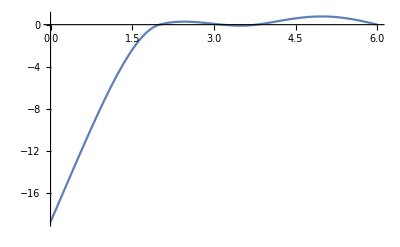

```mathematica
Simplify[((Values@myBeamSolvedV["Solutions"])[[4]]/.)[x]]
Plot[%,{x,0,6.}]
```

Diagrams:

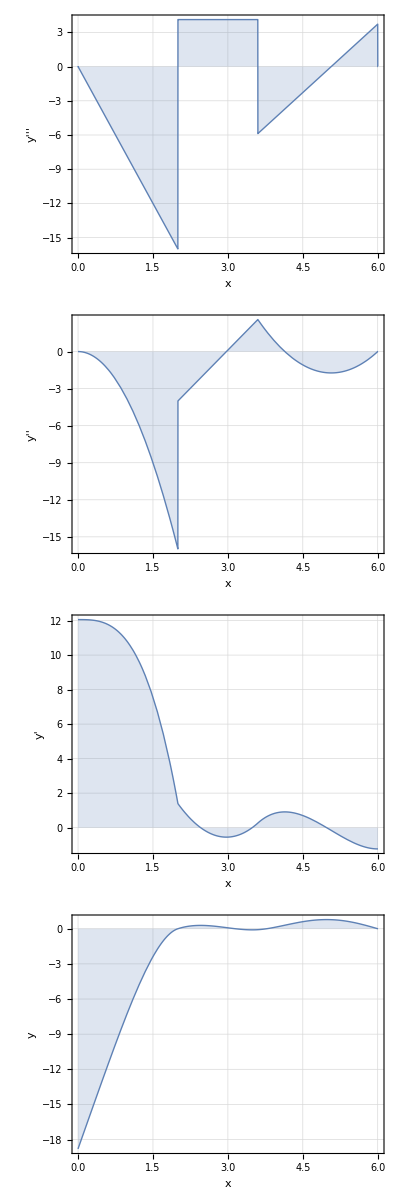

```mathematica
Column@beamPlots@myBeamSolvedV
```

Bending moment extrema:

```mathematica
beamMaxValue[myBeamSolvedV,"y''",{4.,5.5}]
beamMaxValue[myBeamSolvedV,"y''"]
```

{{-1.7298,{x→5.07}}}

{{-16.,{x→2.}}}

Deflection extrema:

```mathematica
beamMaxValue[myBeamSolvedV,"y",{4.,5.5}]
beamMaxValue[myBeamSolvedV,"y"]
```

{{0.780193,{x→4.97685}}}

{{-18.7819,{x→0.}}}

Key feature: analytical solutions

Let’s find out what happens with the beam shape if we move the force P along the beam:

-Graphics-

```mathematica
Manipulate[
Plot[Evaluate[defl//.(Most@myBeamSolved["Numbers"])/.xP->xPP/.],{x,0,6},PlotRange->{Automatic,{-120,40}},Epilog->],{{xPP,3.6,"xP"},0,6.,Appearance->"Open"}]
```

```mathematica
ClearAll@supp
supp[x_,size_]:=
```